```mathematica
(* Copyright (C) 2020 Craciun Alexandru

This package is free: you can redistribute it and/or modify it under the
 terms of the GNU General Public License as published by the Free Software
 Foundation, either version 3 of the License, or (at your option) any
 later version. This program is distributed in the hope that it will be
 useful, but WITHOUT ANY WARRANTY; without even the implied warranty of
 MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE. See the GNU General
 Public License for more details. You should have received a copy of the
 GNU General Public License along with this program
if not, see <https://www.gnu.org/licenses/>.

 Author: CRACIUN Alexandru, e-mail:alexandru.craciun@inflpr.ro

 Please send me an e-mail if you have found a mistake or have questions. *)

(*This code is compatible with Mathematica 10 or later versions.*)

(*Mathematica is (C) Copyright 1988-2020 Wolfram Research, Inc. 
Protected by copyright law and international treaties. 
Unauthorized reproduction or distribution subject to severe civil and criminal penalties.
Mathematica is a registered trademark of Wolfram Research, Inc. 
*)
```

```mathematica
SetOptions[EvaluationNotebook[],AutoStyleOptions->{"CommentStyle"->{FontWeight->Plain,FontColor->Darker[Red],ShowAutoStyles->False,ShowSyntaxStyles->False,AutoNumberFormatting->False,FontFamily->"Consolas"}}]
Off[InterpolatingFunction::dmval]
```

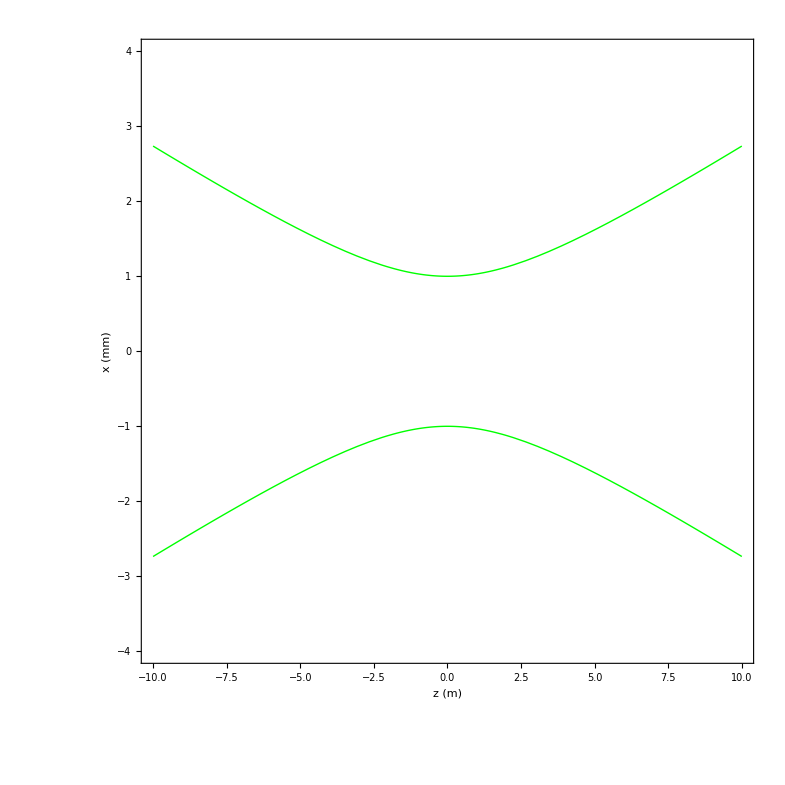

```mathematica
(*Physical Optics - Simple Examples *)

(*Gaussian Beam Ex. 1*)

w=1 mm;(*Beam waist. *)
fGauss[x_,y_]:=Exp[-(x^2+y^2)/w^2];(*Initial Gaussian distribution. *)
ZR=π w^2/waveLength;(*Rayleigh length. *)
Wz[z_]=w √(1+(z/ZR)^2);(*Half of the beam diameter at 1/ⅇ^2 of maxIntensity.*)
Rz[z_]=z(1+(ZR/z)^2);(*Radius of curvature of the wavefront. *)

gaussPlot=Plot[{1,-1}*Wz[z]/mm,{z,-10,10},FrameLabel-> {"z (m)","x (mm)"},PlotRange->{{-10,10},{-4,4}},PlotStyle-> {Green,Thick}]
```

{0.109375,Null}

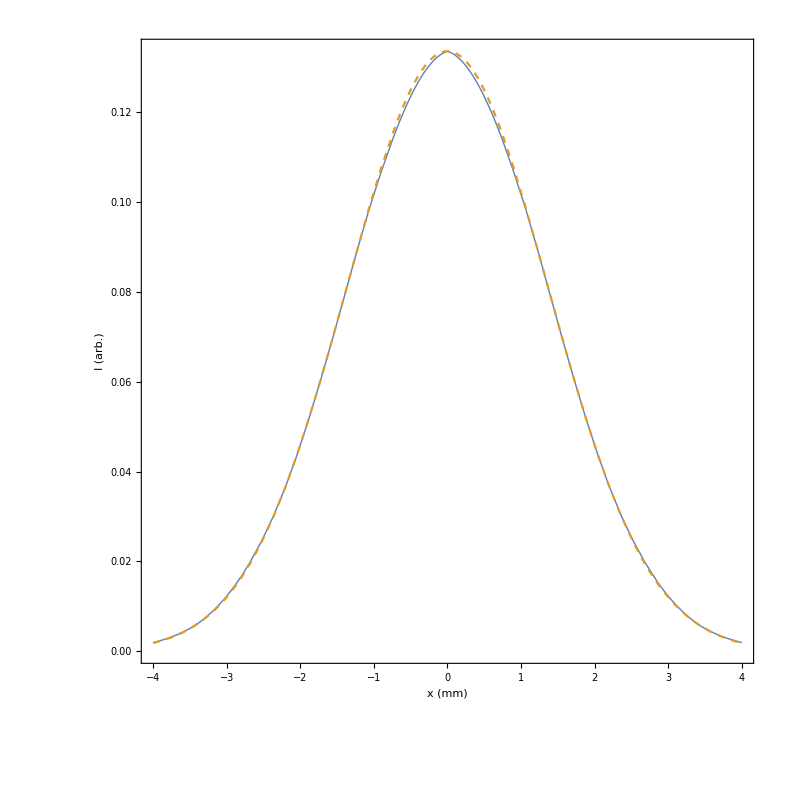

{0.15625,Null}

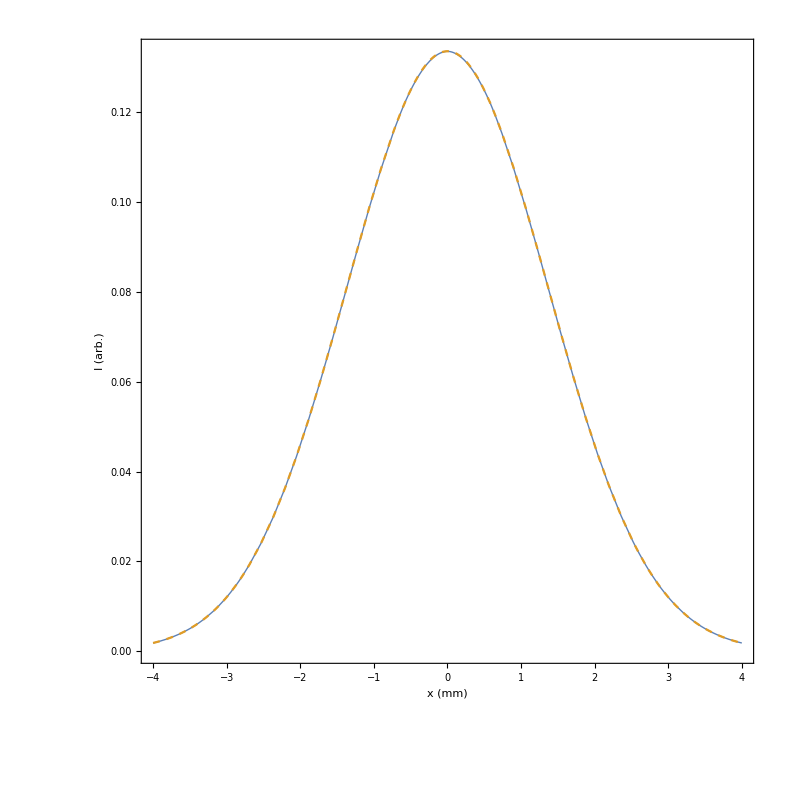

```mathematica
gaussianBeam[x_,y_,z_]=w/Wz[z]*Exp[ⅈ k0 z+ⅈ k0 (x^2+y^2)/(2 Rz[z])-ⅈ ArcTan[z/ZR]-(x^2+y^2)/Wz[z]^2];(*Equation of the Gaussian beam. *)

Timing[f2=FresnelOperator[3.5mm,128,10][fGauss];](*Propagation of the beam having the distribution fGauss using Fresnel diffraction integral. The time needed for the computation is shown. *)

Plot[{Abs[f2[x mm,0]]^2,Abs[gaussianBeam[x mm,0,10]]^2},{x,-4,4},FrameLabel-> {"x (mm)","I (arb.)"},PlotStyle-> {{Automatic,Thick},{Automatic,Dashed}}](*Comparison with the analythical solution. *)

(*OBS1: Sometimes is more time consuming to evaluate the function than to compute the FT, increasing "padLevel" will add 0s around the table of discretized values, which will increase the number of points in the FT grid.*)
(*"padLevel" option is expected to be positive integer. *)

Timing[f2=FresnelOperator[3.5mm,128,10,"padLevel"-> 2][fGauss];](*Propagation of the initial beam with the option "padLevel"-> 2, smoothen the result. *)

Plot[{Abs[f2[x mm,0]]^2,Abs[gaussianBeam[x mm,0,10]]^2},{x,-4,4},FrameLabel-> {"x (mm)","I (arb.)"},PlotStyle-> {{Automatic,Thick},{Automatic,Dashed}}](*Comparison with the analythical solution. *)
```

```mathematica
Timing[fz=SPWOperator[8mm,256,0.1,"nrSteps"-> 220][FresnelOperator[3.5mm,128,-10,"padLevel"-> 2][fGauss]];](*Propagation over the distance 22 m in 220 steps, starting from -10 m, saving the profile for each coordinate z. *)
```

{3.70313,Null}

```mathematica
Show[DensityPlot[Abs[fz[z+10,x mm]]^2,{z,-10,10},{x,-4,4},ColorFunction->colorData97,FrameLabel-> {"z (m)","x (mm)"},PlotPoints-> 250,MaxRecursion->1,PlotRange->All],gaussPlot]
```

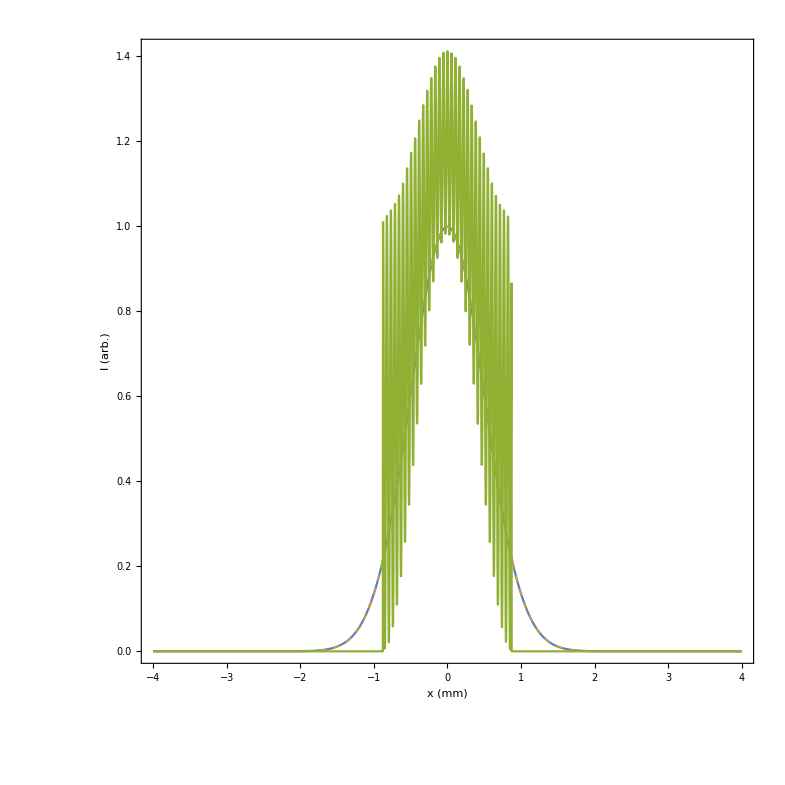

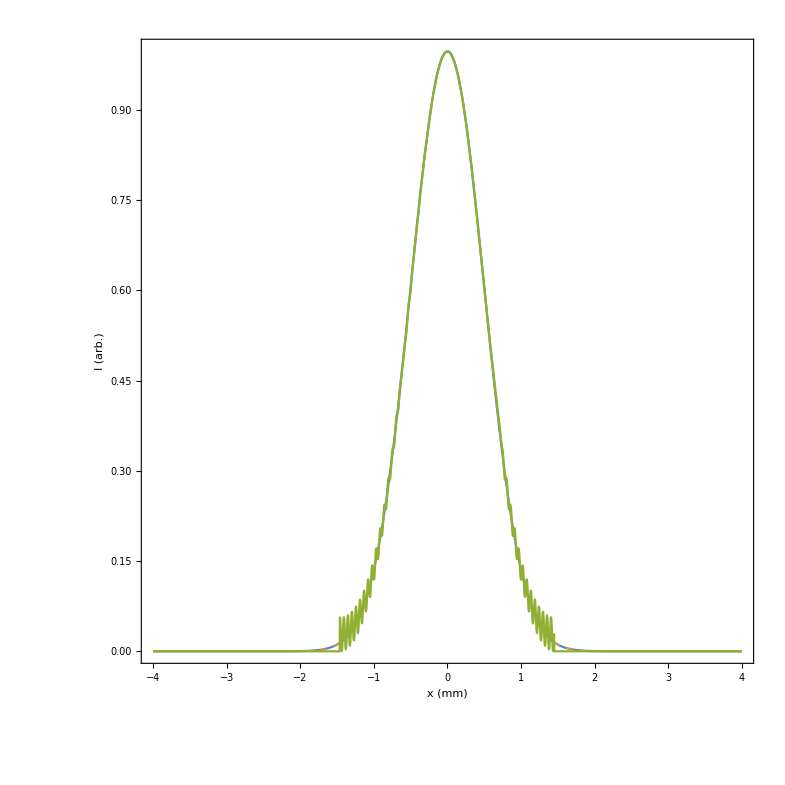

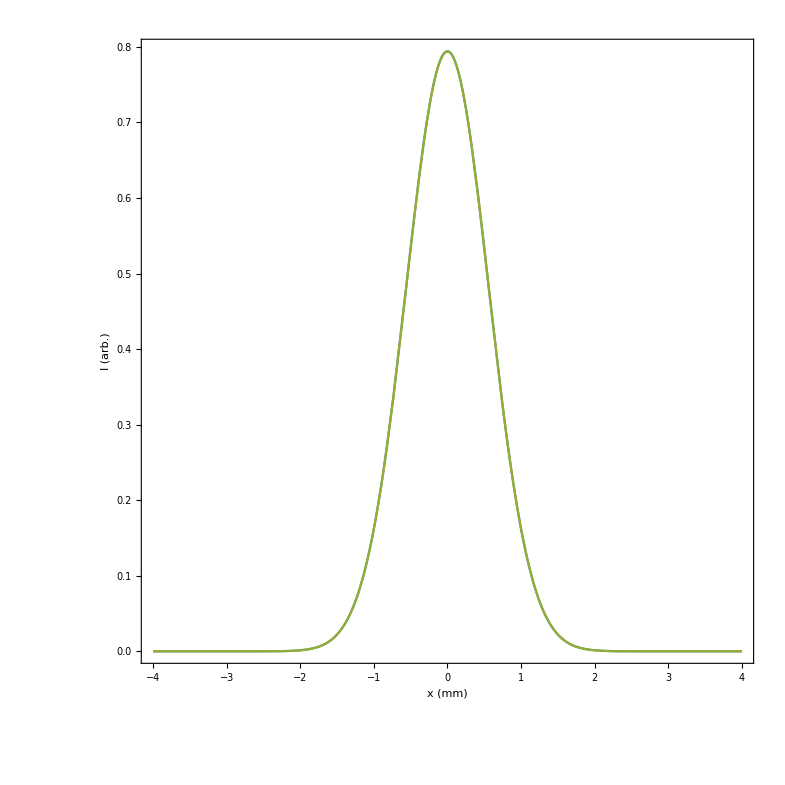

```mathematica
(*OBS2: FresnelOperator does not work for propagation on short distances.*)

f3=SPWOperator[7mm,256,120 mm][fGauss];(*Propagation on 120 mm using Non-Paraxial Angular Spectrum (Spectrum of Plane Waves) method. *)
f4=FresnelOperator[7mm,256,120 mm][fGauss];(*Propagation on 120 mm using Fresnel diffraction integral. *)
Plot[{Abs[gaussianBeam[x mm,0,120 mm]]^2,Abs[f3[x mm,0]]^2,Abs[f4[x mm,0]]^2},{x,-4,4},PlotRange-> All,FrameLabel-> {"x (mm)","I (arb.)"},PlotStyle->{Automatic,{Thick,Dashed},Automatic}]
(*Comparison to the analythical solution, here Fresnel integral does not produce accurate results. *)
f3=SPWOperator[7mm,256,200 mm][fGauss];(*Propagation on 200 mm using Non-Paraxial Angular Spectrum (Spectrum of Plane Waves) method. *)
f4=FresnelOperator[7mm,256,200 mm][fGauss];(*Propagation on 200 mm using Fresnel diffraction integral. *)
Plot[{Abs[gaussianBeam[x mm,0,200 mm]]^2,Abs[f3[x mm,0]]^2,Abs[f4[x mm,0]]^2},{x,-4,4},PlotRange-> All,FrameLabel-> {"x (mm)","I (arb.)"},PlotStyle->{Automatic,{Thick,Dashed},Automatic}]
(*Accuracy of Fresnel diffraction integral increases with z. *)
(*OBS3: SPWOperator is working better for short distances, and is generally accurate on a wider range of parameters.*)
f3=SPWOperator[7mm,256,2000 mm][fGauss];(*Propagation on 2 meters using Non-Paraxial Angular Spectrum (Spectrum of Plane Waves) method. *)
f4=FresnelOperator[7mm,256,2000 mm][fGauss];(*Propagation on 2 meters using Fresnel diffraction integral. *)
Plot[{Abs[gaussianBeam[x mm,0,2000 mm]]^2,Abs[f3[x mm,0]]^2,Abs[f4[x mm,0]]^2},{x,-4,4},PlotRange-> All,FrameLabel-> {"x (mm)","I (arb.)"},PlotStyle->{Automatic,{Thick,Dashed},Automatic}]
(*Both methods are accurate. *)
```

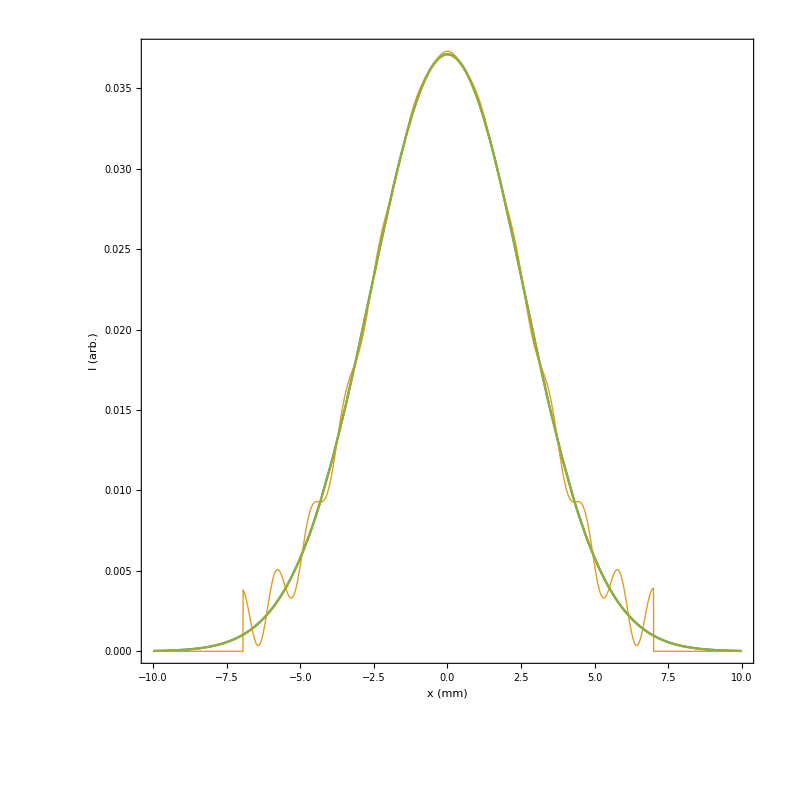

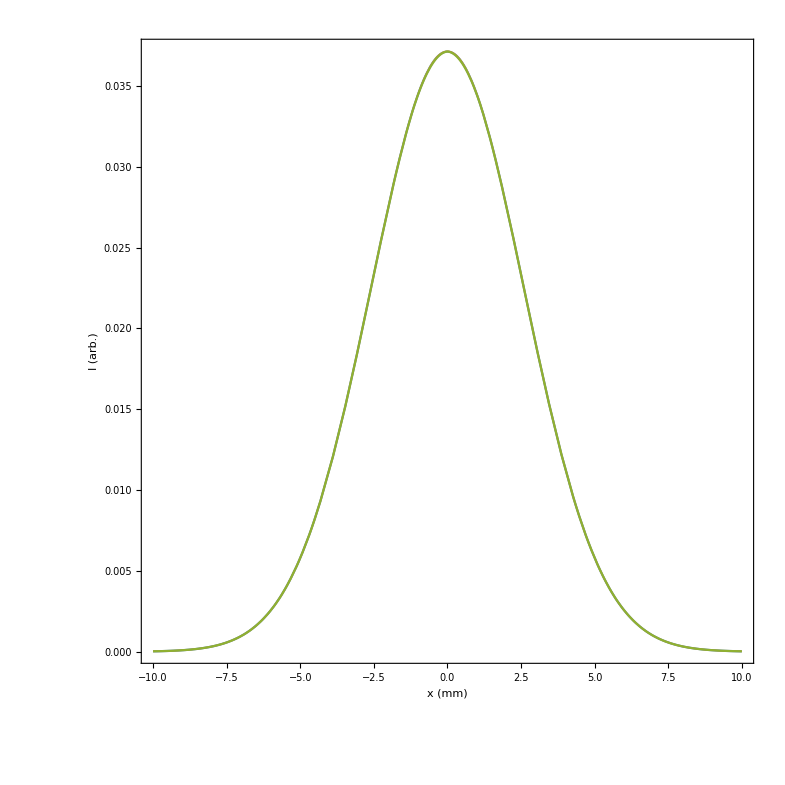

```mathematica
(*OBS4: The domain of definition of the resulted function does not change for SPWOperator unlike for the FresnelOperator. If the beam expand beyond the domain of definition the results are inaccurate.*)
(*      This problem can be solved by padding but more points are necesary. NOTE that "padLevel" have different effects for the two propagation operators. For SPW extends the domain and for Fresnel makes the grid finer. *)
f3=SPWOperator[7mm,256,20][fGauss];(*Propagation on 20 meters using Non-Paraxial Angular Spectrum (Spectrum of Plane Waves) method. *)
f4=FresnelOperator[7mm,256,20][fGauss];(*Propagation on 120 mm using Fresnel diffraction integral. *)
Plot[{Abs[gaussianBeam[x mm,0,20]]^2,Abs[f3[x mm,0]]^2,Abs[f4[x mm,0]]^2},{x,-10,10},PlotRange-> All,FrameLabel-> {"x (mm)","I (arb.)"},PlotStyle->{Automatic,{Thick},Automatic}]
(*Comparison to the analythical solution, in this case Spectrum of Plane Waves method is inaccurate. *)
f3=SPWOperator[7mm,256,20,"padLevel"-> 2][fGauss];(*Propagation on 20 meters using Non-Paraxial Angular Spectrum (Spectrum of Plane Waves) method with padding. *)

Plot[{Abs[gaussianBeam[x mm,0,20]]^2,Abs[f3[x mm,0]]^2,Abs[f4[x mm,0]]^2},{x,-10,10},PlotRange-> All,FrameLabel-> {"x (mm)","I (arb.)"},PlotStyle->{Automatic,{Thick},Automatic}]
(*Now both methods produce accurate results. *)
```